## Exponenciális növekedés kx

```mathematica
p1=2*p
```

2 p

```mathematica
eq= Solve[p1==0,p]
```

{{p→0}}

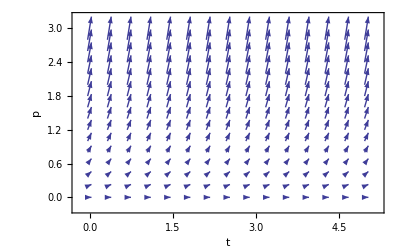

```mathematica
VectorPlot[{1,Evaluate[p1]},{t,0,5},{p,0,3}, Axes->True, AspectRatio->Automatic, AxesLabel->{t,p}]
```

## Egyszerű szaporodás ki ill bevándorlással kx+/-A

```mathematica
p1=p-2
```

-2+p

```mathematica
eq= Solve[p1==0,p]
```

{{p→2}}

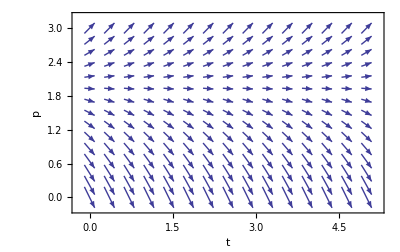

```mathematica
VectorPlot[{1,Evaluate[p1]},{t,0,5},{p,0,3}, Axes->True, AspectRatio->Automatic, AxesLabel->{t,p}]
```

Exponenciálisan növekvő populáció időszakos lehalászással   kx -A

```mathematica
p1 = 2*p - 5
```

-5+2 p

```mathematica
eq = Solve[p1 == 0, p]
```

{{p→5/2}}

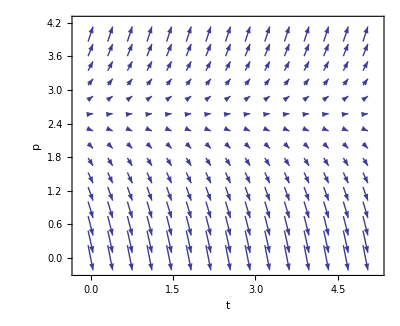

```mathematica
VectorPlot[{1, Evaluate[p1]}, {t, 0, 5}, {p, 0, 4}, Axes -> True, AspectRatio -> Automatic, AxesLabel -> {"t", "p"}]
```

Kihaló populáció indőnkénti betelepítés               -kx+A

```mathematica
p1=-2*p+5
```

5-2 p

```mathematica
eq= Solve[p1==0,p]
```

{{p→5/2}}

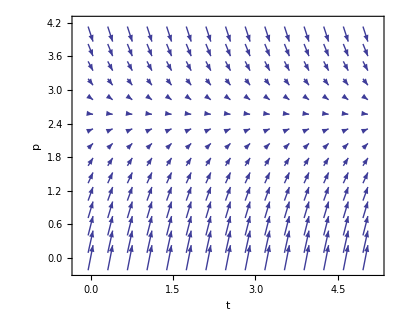

```mathematica
VectorPlot[{1,Evaluate[p1]},{t,0,5},{p,0,4}, Axes->True, AspectRatio->Automatic,AxesLabel->{"t","p"}]
```

## Korlátos növekedés k (A - x)

```mathematica
p1=2(3-p)
```

2 (3-p)

```mathematica
eq= Solve[p1==0,p]
```

{{p→3}}

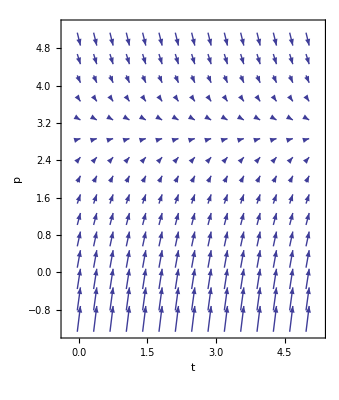

```mathematica
VectorPlot[{1,Evaluate[p1]},{t,0,5},{p,-1,5}, Axes->True, AspectRatio->Automatic, AxesLabel->{t,p}]
```

## Logisztikus modell kx (A - x)

```mathematica
p1=2*p(2-p)
```

2 (2-p) p

```mathematica
eq= Solve[p1==0,p]
```

{{p→0},{p→2}}

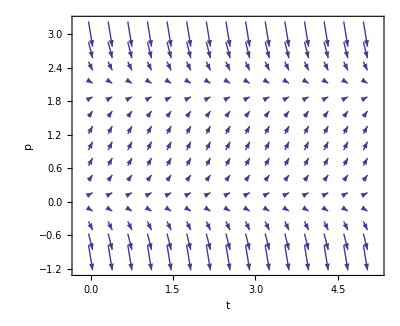

```mathematica
VectorPlot[{1,Evaluate[p1]},{t,0,5},{p,-1,3}, Axes->True, AspectRatio->Automatic,AxesLabel->{"t","p"}]
```

## Logisztikus lehalászás kx(A-x)+B

```mathematica
p1= p(1-p)+2
```

2+(1-p) p

```mathematica
eq= Solve[p1==0,p]
```

{{p→-1},{p→2}}

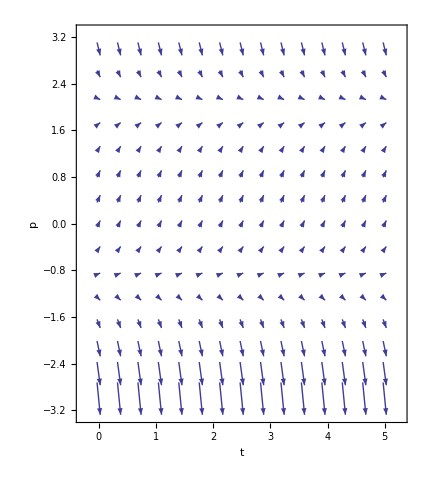

```mathematica
VectorPlot[{1,Evaluate[p1]},{t,0,5},{p,-3,3}, Axes->True, AspectRatio->Automatic,AxesLabel->{"t","p"}]
```